# wbWeinUniBFBcheck

function that gives the couplings according to the UNI and BFB conditions of Weinberg's model.

## Documentation

### Usage

wbWeinUniBFBcheck[mode, options]
wbWeinUniBFBcheck[list, mode, options]

Generate and filter the couplings according to the UNI and BFB conditions using the methods and accuracy prescriptions described in Ref. [1]. Return the list of generated (initial) points and the list of validated points.

### Details & Options

Five accuracy modes are available for BFB filtering:
for mode = 0, the sufficient BFB conditions are imposed using the function wbWeinSufCond
for mode = 1, the necessary 2HDM BFB conditions (NCL1) are imposed using the function wbWeinNecCond1
for mode = 2, the additional necessary BFB conditions (NCL1-NCL3) are imposed using the function wbWeinNecCond2
for mode = 3, the additional necessary BFB conditions (NCL1-NCL4) are imposed using the function wbWeinNecCond3
for mode = 4, the quartic potential is minimized using the function wbMinimFuncPotWein

An initial data set satisfying only the UNI conditions, only the necessary 2HDM BFB conditions (NCL1), or both can be generated by selecting the appropriate options. The initial data set can also be imported via the global parameter “wbParamData” or passed directly to wbWeinUniBFBcheck as a list.

An initial data set satisfying the UNI and BFB conditions can be generated using neural networks by setting the option "NeuralNets"→True.

The following options can be given:

Option | Default value | Meaning
GeneratePoints | True | generates the initial data set
ImposeUNI | True | filter the couplings through the UNI conditions
ImposeBFB | True | filter the couplings athrough the BFB conditions
NeuralNets | False | uses neural networks
ExportData | False | the initial and validated data sets are exported to a file
ShowMessages | True | displays messages reporting the computation times and results
NPoints | 10^3 | number of initial points in the data set
MaxCoupling | 16 | upper bound for each generated coupling
BoundUNI | 8π | unitarity bound
FileNameInit | initial_set.csv | file name for the initial data set
FileNameValid | valid_set.csv | file name for the validated dataset

## Examples

To test usage examples make sure the package has been loaded:

```mathematica
wbLoadBinaries=True; (*wpCompTarget="C";*)
NotebookEvaluate[FileNameJoin[{ParentDirectory@NotebookDirectory[EvaluationNotebook[]],"StableWein.nb"}]]
```

### Basic Examples

The options for wbWeinUniBFBcheck can be set manually:

```mathematica
wbGeneratePoints=True;
wbImposeUNI=True;
wbImposeBFB=True;
wbNeuralNets=False;
wbExportData=False;
wbShowMessages=True;

wbNPoints=1*10^4;
wbMaxCoupling=16;
wbBoundUNI=8*Pi;

wbFileNameInit="initial_set.csv";
wbFileNameValid="valid_set.csv";

wbWeinOpts=Thread[Options[wbWeinUniBFBcheck][[;;,1]]->{wbGeneratePoints,wbImposeUNI,wbImposeBFB,wbNeuralNets,wbExportData,wbShowMessages,wbNPoints,wbMaxCoupling,wbBoundUNI,wbFileNameInit,wbFileNameValid}];
```

Generation of 10^4 points which satisfy only UNI conditions:

```mathematica
{initParamSet,dataUNI}=wbWeinUniBFBcheck[3,"NPoints"->10^4,"ImposeBFB"->False];
```

Run time of data generation (UNI): 0.334556 sec.

In this case, the generated and validated data sets are identical:

```mathematica
initParamSet==dataUNI
```

True

Generation of 10^4 points which satisfy UNI conditions and then filtering according BFB conditions with mode = 3:

```mathematica
{initParamSet,dataNec3}=wbWeinUniBFBcheck[3,wbWeinOpts];
```

Run time of data generation (UNI+Nec1): 4.27548 sec.

Run time of the BFB enforcement (mode 3): 1.89819 sec.

BFB points: 7459

Fractions of points satisfying the BFB conditions:

```mathematica
{initParamSet,dataNec1}=wbWeinUniBFBcheck[1,"ShowMessages"->False];
wbParamData=initParamSet;
{initParamSet,dataSuf}=wbWeinUniBFBcheck[0,"GeneratePoints"->False,"ShowMessages"->False];
{initParamSet,dataNec2}=wbWeinUniBFBcheck[2,"GeneratePoints"->False,"ShowMessages"->False];
{initParamSet,dataNec3}=wbWeinUniBFBcheck[3,"GeneratePoints"->False,"ShowMessages"->False];
Length/@{dataNec1,dataSuf,dataNec2,dataNec3}
PercentForm/@N[%/Length[wbParamData]]
```

{1000,577,754,749}

{100%,57.7%,75.4%,74.9%}

### Scope

Couplings are generated in the range ∣coupling∣ ≤ 10 and are then filtered to retain only those that satisfy the relevant BFB conditions.

```mathematica
optTMP=wbOptChange[wbWeinOpts,{"GeneratePoints","ImposeUNI"},{False,False}];
```

```mathematica
{initParamSet,dataNec1}=wbWeinUniBFBcheck[1,"NPoints"->10^6,"MaxCoupling"->10,"ImposeUNI"->False];
wbParamData=dataNec1;
{initParamSet,dataNec2}=wbWeinUniBFBcheck[2,optTMP];
{initParamSet,dataNec3}=wbWeinUniBFBcheck[3,optTMP];
Length/@{dataNec1,dataNec2,dataNec3}
PercentForm/@N[%/Length[wbParamData]]
```

Run time of data generation (NCL1): 1.59002 sec.

BFB points: 1000000

Run time of the BFB enforcement (mode 2): 13.2766 sec.

BFB points: 945270

Run time of the BFB enforcement (mode 3): 57.835 sec.

BFB points: 943193

{1000000,945270,943193}

{100%,94.53%,94.32%}

```mathematica
parNames={"a_1","a_2","a_3","b_1","b_2","b_3","c_1","c_2","c_3","d_1","d_2","d_3","ϵ"};
table1=TableForm[Round[#,10.^-2]&/@(MinMax/@Transpose@dataNec1),TableHeadings->{parNames,{"Min","Max"}}]; 
table2=TableForm[Round[#,10.^-2]&/@(MinMax/@Transpose@dataNec2),TableHeadings->{parNames,{"Min","Max"}}]; 
table3=TableForm[Round[#,10.^-2]&/@(MinMax/@Transpose@dataNec3),TableHeadings->{parNames,{"Min","Max"}}];
Grid[#,Spacings->{0, 1}]&/@(Partition[#,1]&/@Transpose[{{"mode = 1","mode = 2","mode = 3"},{table1,table2,table3}}]);
Grid[{%},Spacings->{4, 0}]
```

mode = 1
 | Min | Max
a_1 | 0. | 10.
a_2 | 0. | 10.
a_3 | 0. | 10.
b_1 | -9.9 | 10.
b_2 | -9.88 | 10.
b_3 | -9.79 | 10.
c_1 | -10. | 10.
c_2 | -10. | 10.
c_3 | -10. | 10.
d_1 | -10. | 10.
d_2 | -10. | 10.
d_3 | -10. | 10.
ϵ | 0. | 6.28 | mode = 2
 | Min | Max
a_1 | 0. | 10.
a_2 | 0. | 10.
a_3 | 0. | 10.
b_1 | -9.9 | 10.
b_2 | -9.88 | 10.
b_3 | -9.79 | 10.
c_1 | -10. | 10.
c_2 | -10. | 10.
c_3 | -10. | 10.
d_1 | -10. | 10.
d_2 | -10. | 10.
d_3 | -10. | 10.
ϵ | 0. | 6.28 | mode = 3
 | Min | Max
a_1 | 0. | 10.
a_2 | 0. | 10.
a_3 | 0. | 10.
b_1 | -9.9 | 10.
b_2 | -9.88 | 10.
b_3 | -9.79 | 10.
c_1 | -10. | 10.
c_2 | -10. | 10.
c_3 | -10. | 10.
d_1 | -10. | 10.
d_2 | -10. | 10.
d_3 | -10. | 10.
ϵ | 0. | 6.28

Distribution of the couplings filtered using mode = 1 (green contour), mode = 2 (blue dashed contour), and mode = 3 (red dashed contour):

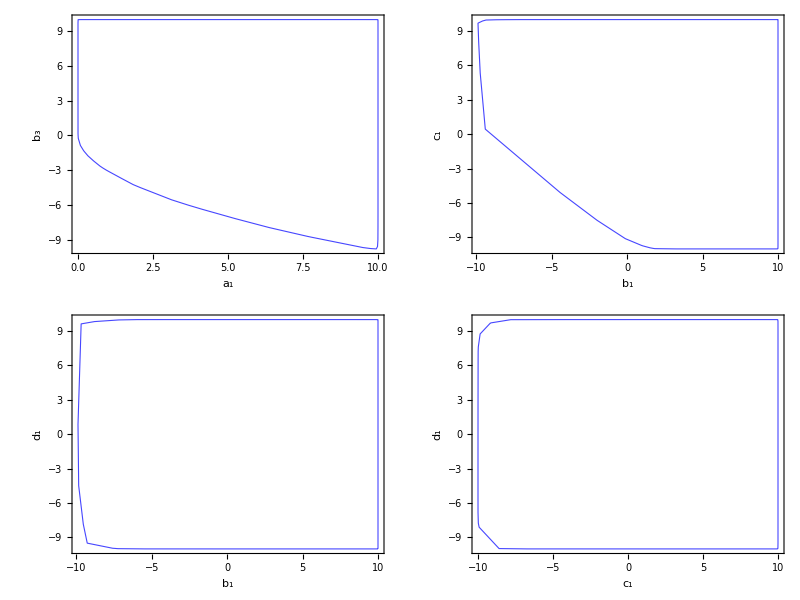

```mathematica
Table[Show[{ConvexHullMesh[dataNec1[[;;,xx]],MeshCellStyle->{1->{Darker[Green,0.2]},2->Opacity[0,Green]}],ConvexHullMesh[dataNec2[[;;,xx]],MeshCellStyle->{1->{Lighter[Blue,0.2],Dashing[{0.09,0.03}],Opacity[0.9]},2->Opacity[0,Blue]}],ConvexHullMesh[dataNec3[[;;,xx]],MeshCellStyle->{1->{Red,Dashing[{0.01,0.01}]},2->Opacity[0,Red]}]},PlotRange->Automatic,Frame->True,AspectRatio->1,FrameStyle->Black,ImageSize->250,FrameLabel->{Style[parNames⟦xx[[1]]⟧,16,Black],Style[parNames⟦xx[[2]]⟧,16,Black]},Epilog->{Inset[(*Framed[#,Background->White,FrameStyle->Black,RoundingRadius->10]&@*)Graphics[makePlotLegend[{"mode 1","mode 2","mode 3"},{Graphics[{Thickness[0.04],Darker[Green,0.2],Line[{{-1,0},{0,0}}]}],Graphics[{Thickness[0.04],Dashing[{0.45,0.08}],Lighter[Blue,0.2],Line[{{-1,0},{0,0}}]}],Graphics[{Thickness[0.04],Dashing[{0.1,0.1}],Red,Line[{{-1,0},{0,0}}]}]},{-0.08,1.1},30,12,FontFamily->"Times"],PlotRange->{{0,0.08},{0,0.04}},ImageSize->80],Scaled[{0.27,0.83}]]}],{xx,{{1,6},{4,7},{4,10},{7,10}}}];
Grid[Partition[%,2]]
```

Couplings are generated to satisfy the UNI and NCL1 conditions, and are then filtered to retain only those that also satisfy the NCL2-NCL3 or NCL4 BFB conditions:

```mathematica
optTMP=wbOptChange[wbWeinOpts,{"GeneratePoints","ImposeUNI"},{False,False}];
```

```mathematica
{initParamSet,dataUniNec1}=wbWeinUniBFBcheck[1,"NPoints"->10^6];
wbParamData=dataUniNec1;
{initParamSet,dataUniNec2}=wbWeinUniBFBcheck[2,optTMP];
{initParamSet,dataUniNec3}=wbWeinUniBFBcheck[3,optTMP];
Length/@{dataUniNec1,dataUniNec2,dataUniNec3}
PercentForm/@N[%/Length[wbParamData]]
```

Run time of data generation (UNI+NCL1): 379.607 sec.

BFB points: 1000000

Run time of the BFB enforcement (mode 2): 17.4287 sec.

BFB points: 752556

Run time of the BFB enforcement (mode 3): 110.401 sec.

BFB points: 747834

{1000000,752556,747834}

{100%,75.26%,74.78%}

```mathematica
{initParamSet,dataUniNec1}=wbWeinUniBFBcheck[1,"NPoints"->10^6];
wbParamData=dataUniNec1;
{initParamSet,dataUniNec2}=wbWeinUniBFBcheck[2,optTMP];
{initParamSet,dataUniNec3}=wbWeinUniBFBcheck[3,optTMP];
Length/@{dataUniNec1,dataUniNec2,dataUniNec3}
PercentForm/@N[%/Length[wbParamData]]
```

```mathematica
{initParamSet,dataUniNec1}=wbWeinUniBFBcheck[1,"NPoints"->10^6];
```

```mathematica
parNames={"a_1","a_2","a_3","b_1","b_2","b_3","c_1","c_2","c_3","d_1","d_2","d_3","ϵ"};
table1=TableForm[Round[#,10.^-2]&/@(MinMax/@Transpose@dataUniNec1),TableHeadings->{parNames,{"Min","Max"}}]; 
table2=TableForm[Round[#,10.^-2]&/@(MinMax/@Transpose@dataUniNec2),TableHeadings->{parNames,{"Min","Max"}}]; 
table3=TableForm[Round[#,10.^-2]&/@(MinMax/@Transpose@dataUniNec3),TableHeadings->{parNames,{"Min","Max"}}];
Grid[#,Spacings->{0, 1}]&/@(Partition[#,1]&/@Transpose[{{"mode = 1","mode = 2","mode = 3"},{table1,table2,table3}}]);
Grid[{%},Spacings->{4, 0}]
```

mode = 1
 | Min | Max
a_1 | 0. | 8.37
a_2 | 0. | 8.37
a_3 | 0. | 8.37
b_1 | -7.68 | 15.45
b_2 | -7.66 | 15.64
b_3 | -7.52 | 16.06
c_1 | -15.49 | 15.72
c_2 | -15.75 | 15.99
c_3 | -15.58 | 15.74
d_1 | -8.21 | 8.14
d_2 | -8.11 | 8.12
d_3 | -8.23 | 8.13
ϵ | 0. | 6.28 | mode = 2
 | Min | Max
a_1 | 0. | 8.37
a_2 | 0. | 8.37
a_3 | 0. | 8.37
b_1 | -7.24 | 15.45
b_2 | -7.34 | 15.64
b_3 | -7.28 | 16.06
c_1 | -15.49 | 15.56
c_2 | -15.46 | 15.43
c_3 | -15.48 | 15.02
d_1 | -7.97 | 7.91
d_2 | -8.02 | 8.05
d_3 | -7.88 | 7.94
ϵ | 0. | 6.28 | mode = 3
 | Min | Max
a_1 | 0. | 8.37
a_2 | 0. | 8.37
a_3 | 0. | 8.37
b_1 | -7.24 | 15.45
b_2 | -7.34 | 15.64
b_3 | -7.28 | 16.06
c_1 | -15.49 | 15.56
c_2 | -15.46 | 15.43
c_3 | -15.48 | 15.02
d_1 | -7.97 | 7.91
d_2 | -8.02 | 8.05
d_3 | -7.88 | 7.94
ϵ | 0. | 6.28

Distribution of the couplings satisfying UNI conditions and filtered using mode = 1 (green contour), mode = 2 (blue dashed contour), and mode = 3 (red dashed contour):

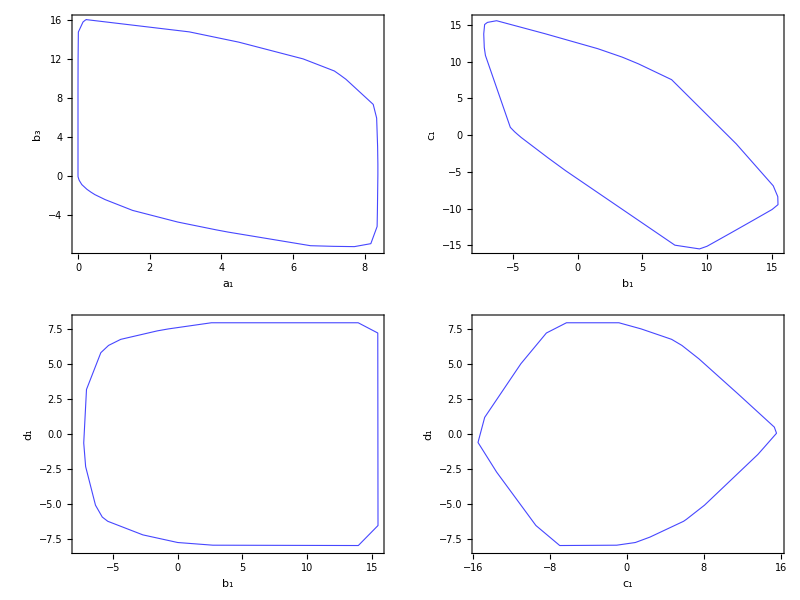

```mathematica
Table[Show[{ConvexHullMesh[dataUniNec1[[;;,xx]],MeshCellStyle->{1->{Darker[Green,0.2]},2->Opacity[0,Green]}],ConvexHullMesh[dataUniNec2[[;;,xx]],MeshCellStyle->{1->{Lighter[Blue,0.2],Dashing[{0.09,0.03}],Opacity[0.9]},2->Opacity[0,Blue]}],ConvexHullMesh[dataUniNec3[[;;,xx]],MeshCellStyle->{1->{Red,Dashing[{0.01,0.01}]},2->Opacity[0,Red]}]},PlotRange->Automatic,Frame->True,AspectRatio->1,FrameStyle->Black,ImageSize->250,FrameLabel->{Style[parNames⟦xx[[1]]⟧,16,Black],Style[parNames⟦xx[[2]]⟧,16,Black]},Epilog->{Inset[(*Framed[#,Background->White,FrameStyle->Black,RoundingRadius->10]&@*)Graphics[makePlotLegend[{"mode 1","mode 2","mode 3"},{Graphics[{Thickness[0.04],Darker[Green,0.2],Line[{{-1,0},{0,0}}]}],Graphics[{Thickness[0.04],Dashing[{0.45,0.08}],Lighter[Blue,0.2],Line[{{-1,0},{0,0}}]}],Graphics[{Thickness[0.04],Dashing[{0.1,0.1}],Red,Line[{{-1,0},{0,0}}]}]},{-0.08,1.1},30,12,FontFamily->"Times"],PlotRange->{{0,0.08},{0,0.04}},ImageSize->80],Scaled[{0.35,0.65}]]}],{xx,{{1,6},{4,7},{4,10},{7,10}}}];
Grid[Partition[%,2]]
```

To improve the accuracy of the scan over the orbit-space surface (mode 3), the scanning grid can be refined by adjusting the parameter values of stepsWein. Note that increasing these values also increases the computation time. For most practical applications (≈99.99% accuracy), the default settings (stepsWein = {17, 40, 0}) are sufficient; however, to achieve near-100% accuracy it may be necessary to increase them, for example to stepsWein = {30, 100, 50}.

By default, the global parameters (wbfaceListWein, wbθListWein, and wbθListWein2) of function wbWeinNecCond3 specify the following numbers of grid points:

```mathematica
Length/@{wbfaceListWein,wbθListWein,wbθListWein2}
```

{5148,75113,0}

which enables relatively fast filtering of BFB-allowed points:

```mathematica
wbParamData=ParallelTable[wbWeinParRndNec[10],{10^6}];
```

```mathematica
{initParamSet,dataNec3}=wbWeinUniBFBcheck[3,"GeneratePoints"->False,"ImposeUNI"->False];
```

Run time of the BFB enforcement (mode 3): 28.0451 sec.

BFB points: 87888

Using wbWeinGridGen, we increase the number of grid points:

```mathematica
stepsWein={27,80,30};
{wbfaceListWein,wbθListWein,wbθListWein2}=wbWeinGridGen[stepsWein];
```

Number of points in Weinberg's grids: {20000, 585497, 557}

which allows BFB-allowed points to be filtered more accurately, at the cost of increased computational time:

```mathematica
{initParamSet,dataNec3}=wbWeinUniBFBcheck[3,"GeneratePoints"->False,"ImposeUNI"->False];
```

Run time of the BFB enforcement (mode 3): 212.182 sec.

BFB points: 87887

Note that wbWeinUniBFBcheck with mode = 3 yields highly accurate results even with the default grids because it operates in combination with wbWeincSufCond and wbWeinNecCond2.

The default grid points wbfaceListWein on the surface of the phase space:

```mathematica
labels=Style[#,Black,13]&/@{"P_1","P_2","P_3","P_4"};
pointPos={{1,0,0},{0,1,0},{0,0,1},{1,1,1}};
labPos={{0.95,0,0},{0,0.95,0},{0,0,1},{1,1,1}};
Show[{Plot3D[{(√(w2*w3)-√((1-w2)*(1-w3)))^2,(√(w2*w3)+√((1-w2)*(1-w3)))^2},{w2,0,1},{w3,0,1},PlotStyle->Directive[Opacity[0.95],Lighter[Blue,0.9],Specularity[White,70]]],ListLinePlot3D[{{0,0,1},{1,1,1},{1,0,0},{0,0,1},{0,1,0},{1,1,1}},PlotRange->All,PlotStyle->{Directive[Darker[Red,0.0],Dashed,Thickness[0.003]]}],ListLinePlot3D[{{0,1,0},{1,0,0}},PlotRange->All,PlotStyle->{Directive[Darker[Red,0.0],Dashed,Thickness[0.003]]}],ListPointPlot3D[wbfaceListWein,PlotRange->All,AspectRatio->0.9,ImageSize->400,PlotStyle->{Directive[Darker[Blue,0.1],PointSize->0.007]}],ListPointPlot3D[Table[Callout[pointPos[[x]],labels[[x]],labPos[[x]],Appearance->"CurvedLeader"],{x,1,Length[labels]}],PlotStyle->Directive[Black,PointSize->0.009]]},BoxRatios->{1,1,1},PlotRange->{{0,1},{0,1},{0,1}},AspectRatio->0.9,ImageSize->400,PlotStyle->{Directive[Darker[Red,0.1],PointSize->0.007],Directive[Darker[Blue,0.1],PointSize->0.007]},AxesLabel->fLabelSty/@{"ϖ_1","ϖ_2","ϖ_3"}]
```

-Graphics3D-

With mode = 4, the points in the initial data set are validated by minimizing the quartic potential using wbMinimFuncPotWein. This mode is useful for cross-checking the BFB-validated points obtained with mode = 3 and for achieving maximal accuracy. However, potential minimization is computationally expensive and requires substantial resources:

```mathematica
{initParamSet,dataNec3}=wbWeinUniBFBcheck[3,"NPoints"->10^4];
```

Run time of data generation (UNI+Nec1): 3.8952 sec.

Run time of the BFB enforcement (mode 3): 1.78604 sec.

BFB points: 7521

```mathematica
wbParamData=dataNec3;
{initParamSet,validParamSet}=wbWeinUniBFBcheck[4,"GeneratePoints"->False];
```

Run time of the potential minimization (mode 4): 357.207 sec.

BFB points: 7521

Branco’s model (wbBrancUniBFBcheck) is a special case of Weinberg’s model (wbWeinUniBFBcheck) obtained by setting the phase ϵ = 0 (the CP-conserving case):

```mathematica
{initParamSet,dataNec3Branc}=wbBrancUniBFBcheck[3,"NPoints"->10^4];
```

Run time of data generation (UNI+Nec1): 3.68887 sec.

Run time of the BFB enforcement (mode 3): 0.415987 sec.

BFB points: 7608

```mathematica
wbParamData=Join[#,{0}]&/@initParamSet;
```

```mathematica
{initParamSet,dataNec3Wein}=wbWeinUniBFBcheck[3,"GeneratePoints"->False];
```

Run time of the BFB enforcement (mode 3): 1.84467 sec.

BFB points: 7608

```mathematica
dataNec3Branc==dataNec3Wein[[;;,;;-2]]
```

True

Although wbWeinUniBFBcheck produces the same results, wbBrancUniBFBcheck is more optimized for the CP-conserving case, as reflected by the BFB-enforcement runtimes reported above.

### Options

#### Setting options

The default options for wbWeinUniBFBcheck can be modified either directly in the package file “StableWein.nb” or by using SetOptions[wbWeinUniBFBcheck, ...]]:

```mathematica
SetOptions[wbWeinUniBFBcheck,"NPoints"->10^5]
```

{GeneratePoints→True,ImposeUNI→True,ImposeBFB→True,NeuralNets→False,ExportData→False,ShowMessages→True,NPoints→100000,MaxCoupling→16,BoundUNI→8 π,FileNameInit→initial_set.csv,FileNameValid→valid_set.csv}

The option list for wbWeinUniBFBcheck can be created as follows:

```mathematica
wbGeneratePoints=True;
wbImposeUNI=True;
wbImposeBFB=True;
wbNeuralNets=False;
wbExportData=False;
wbShowMessages=True;

wbNPoints=1*10^4;
wbMaxCoupling=16;
wbBoundUNI=8*Pi;

wbFileNameInit="initial_set.csv";
wbFileNameValid="valid_set.csv";

wbWeinOpts=Thread[Options[wbWeinUniBFBcheck][[;;,1]]->{wbGeneratePoints,wbImposeUNI,wbImposeBFB,wbNeuralNets,wbExportData,wbShowMessages,wbNPoints,wbMaxCoupling,wbBoundUNI,wbFileNameInit,wbFileNameValid}];
```

A temporary option list can be created by modifying the default options or a previously defined option list using function wbOptChange:

```mathematica
optTMP=wbOptChange[Options[wbWeinUniBFBcheck],{"GeneratePoints","ImposeUNI"},{False,False}]
```

{GeneratePoints→False,ImposeUNI→False,ImposeBFB→True,NeuralNets→False,ExportData→False,ShowMessages→True,NPoints→1000,MaxCoupling→16,BoundUNI→8 π,FileNameInit→initial_set.csv,FileNameValid→valid_set.csv}

```mathematica
optTMP=wbOptChange[wbWeinOpts,{"ExportData","ImposeBFB","NPoints","MaxCoupling","BoundUNI"},{True,False,10^2,35,16 π}]
```

{GeneratePoints→True,ImposeUNI→True,ImposeBFB→False,NeuralNets→False,ExportData→True,ShowMessages→True,NPoints→100,MaxCoupling→35,BoundUNI→16 π,FileNameInit→initial_set.csv,FileNameValid→valid_set.csv}

```mathematica
{initParamSet,validParamSet}=wbWeinUniBFBcheck[1,optTMP];
MinMax/@Transpose@initParamSet
```

Run time of data generation (UNI): 0.369773 sec.

{{-16.3051,14.3379},{-13.5926,14.9801},{-14.5407,13.7513},{-26.208,29.15},{-22.3939,24.4959},{-29.5022,24.9818},{-28.0508,26.1465},{-22.7297,29.2856},{-26.5998,28.017},{-14.716,12.5386},{-15.3424,16.3015},{-14.413,14.4678},{0.0726799,6.12636}}

#### GeneratePoints

By default, wbWeinUniBFBcheck generates an initial data set with the appropriate conditions imposed. Here, we generate 10^4 points that satisfy only the UNI conditions:

```mathematica
{initParamSet,dataUNI}=wbWeinUniBFBcheck[1,"NPoints"->10^4,"ImposeBFB"->False];
```

Run time of data generation (UNI): 0.347414 sec.

The initial data set can be imported via the global parameter “wbParamData” and then filtered using the desired conditions. Here, we filter a previously generated data set using the BFB conditions with mode = 3:

```mathematica
wbParamData=dataUNI;
{initParamSet,dataNec3}=wbWeinUniBFBcheck[3,"GeneratePoints"->False];
```

Run time of the BFB enforcement (mode 3): 0.898128 sec.

BFB points: 19

Alternatively, the imported data can be passed directly to wbWeinUniBFBcheck (note that the option "GeneratePoints" → False can be omitted):

```mathematica
{initParamSet,dataNec3}=wbWeinUniBFBcheck[dataUNI,3];
```

Run time of the BFB enforcement (mode 3): 0.869472 sec.

BFB points: 19

#### ImposeUNI

By default, wbWeinUniBFBcheck generates or filters an initial data set with the UNI conditions imposed. By setting "ImposeUNI" → False, an initial data set satisfying only the NCL1 conditions is generated:

```mathematica
{initParamSet,validParamSet}=wbWeinUniBFBcheck[1,"ImposeUNI"->False];
```

Run time of data generation (Nec1): 0.069349 sec.

By setting both "ImposeUNI" → False and "ImposeBFB" → False, an initial dataset with randomized couplings is generated:

```mathematica
{initParamSet,validParamSet}=wbWeinUniBFBcheck[1,"ImposeUNI"->False,"ImposeBFB"->False];
```

Run time of data generation (parRnd): 0.06745 sec.

#### ImposeBFB

By default, wbWeinUniBFBcheck generates or filters an initial data set with the necessary 2HDM BFB  conditions imposed. By setting "ImposeBFB" → False, an initial data set satisfying only the UNI conditions is generated:

```mathematica
{initParamSet,validParamSet}=wbWeinUniBFBcheck[1,"ImposeBFB"->False];
```

Run time of data generation (UNI): 0.105175 sec.

If "ImposeBFB" → False is set, the BFB accuracy modes are disabled:

```mathematica
{initParamSet,validParamSet}=wbWeinUniBFBcheck[3,"ImposeBFB"->False];
```

Run time of data generation (UNI): 0.134557 sec.

#### NeuralNets

When neural networks are enabled in wbWeinUniBFBcheck, they predict parameter points that satisfy the UNI and BFB conditions. If "ImposeBFB" → True is set, the predicted data set is subsequently validated using the selected BFB method(s), whereas the UNI check is already incorporated into the neural network generation step.

```mathematica
optTMP=wbOptChange[wbWeinOpts,{"NeuralNets","NPoints"},{True,2000}];
```

```mathematica
{initParamSet,validParamSet}=wbWeinUniBFBcheck[1,optTMP];
```

Run time of nets prediction: 3.69681 sec.

Run time of the BFB enforcement (mode 1): 0.057593 sec.

BFB points: 2158

Accuracy of NNs: 100.%

```mathematica
{initParamSet,validParamSet}=wbWeinUniBFBcheck[2,optTMP];
```

Run time of nets prediction: 3.72673 sec.

Run time of the BFB enforcement (mode 2): 0.123867 sec.

BFB points: 2135

Accuracy of NNs: 99.9532%

```mathematica
{initParamSet,validParamSet}=wbWeinUniBFBcheck[3,optTMP];
```

Run time of nets prediction: 4.03027 sec.

Run time of the BFB enforcement (mode 3): 0.961678 sec.

BFB points: 2213

Accuracy of NNs: 99.9548%

The neural network inference time is slightly longer than the total runtime of our proposed method (UNI + NCL1-NCL4):

```mathematica
{initParamSet,validParamSet}=wbWeinUniBFBcheck[3,"NPoints"->2900];
```

Run time of data generation (UNI+Nec1): 1.21445 sec.

Run time of the BFB enforcement (mode 3): 1.00229 sec.

BFB points: 2148

however, it is much shorter than that of the conventional approach based on numerical minimization of the potential.

```mathematica
{initParamSet,validParamSet}=wbWeinUniBFBcheck[4,"NPoints"->2900];
```

Run time of data generation (UNI+Nec1): 1.21717 sec.

Run time of the potential minimization (mode 4): 112.204 sec.

BFB points: 2204

The parameter distributions are similar for points generated by the neural network predictor and for those obtained using the UNI and necessary BFB conditions:

```mathematica
{initParamSet,validParamSet}=wbWeinUniBFBcheck[3,"NPoints"->IntegerPart[4/3*10^6]];
```

Run time of data generation (UNI+Nec1): 511.906 sec.

Run time of the BFB enforcement (mode 3): 139.7 sec.

BFB points: 998496

```mathematica
{initParamSet,validParamNets}=wbWeinUniBFBcheck[3,"NeuralNets"->True,"NPoints"->10^6];
```

Run time of nets prediction: 1338.11 sec.

Run time of the BFB enforcement (mode 3): 121.01 sec.

BFB points: 1010734

Accuracy of NNs: 99.926%

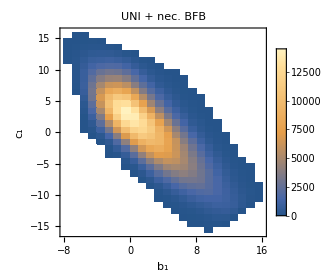
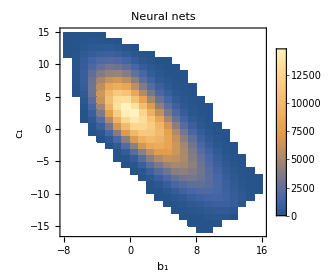
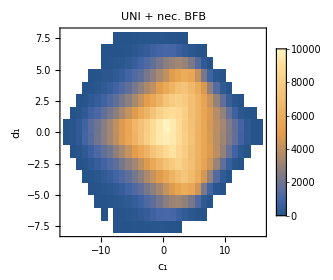
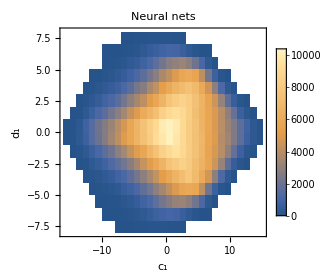
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
parNames={"a_1","a_2","a_3","b_1","b_2","b_3","c_1","c_2","c_3","d_1","d_2","d_3","ϵ"};
Table[{Show[{DensityHistogram[validParamSet[[;;,xx]],ChartLegends->Automatic,PerformanceGoal->"Quality",PlotLabel->"UNI + nec. BFB"],ConvexHullMesh[validParamSet[[;;,xx]],MeshCellStyle->{1->{Green},2->Opacity[0]}]},PlotRange->Automatic,Frame->True,AspectRatio->1,FrameStyle->Black,ImageSize->280,FrameLabel->{Style[parNames⟦xx[[1]]⟧,16,Black],Style[parNames⟦xx[[2]]⟧,16,Black]}],Show[{DensityHistogram[validParamNets[[;;,xx]],ChartLegends->Automatic,PerformanceGoal->"Quality",PlotLabel->"Neural nets"],ConvexHullMesh[validParamNets[[;;,xx]],MeshCellStyle->{1->{Red},2->Opacity[0]}]},PlotRange->Automatic,Frame->True,AspectRatio->1,FrameStyle->Black,ImageSize->280,FrameLabel->{Style[parNames⟦xx[[1]]⟧,16,Black],Style[parNames⟦xx[[2]]⟧,16,Black]}]},{xx,{{4,7},{7,10}}}];
Grid[%]
```

#### Import & Export Data

Because many data formats are possible, we allow users to import the data into Mathematica themselves. The imported data can then be passed to wbWeinUniBFBcheck by setting the global parameter wbParamData.

```mathematica
initFile=Import[ParentDirectory@ParentDirectory[NotebookDirectory[]]<>"/Data/initial_set.csv"];
```

```mathematica
wbParamData=initFile;
{initParamSet,dataNec3}=wbWeinUniBFBcheck[3,"GeneratePoints"->False];
```

Run time of the BFB enforcement (mode 3): 0.948726 sec.

BFB points: 755

Alternatively, the imported data can be passed directly to wbWeinUniBFBcheck (note that the option "GeneratePoints" → False can be omitted):

```mathematica
{initParamSet,dataNec3}=wbWeinUniBFBcheck[initFile,3];
```

Run time of the BFB enforcement (mode 3): 0.990178 sec.

BFB points: 755

By setting "ExportData" → True, an initial and validated data sets are exported to the folder “Data”, with file names specified by the "FileNameInit" and "FileNameValid" options:

```mathematica
{initParamSet,validParamSet}=wbWeinUniBFBcheck[2,"ExportData"->True,"FileNameInit"->"init1.csv","FileNameValid"->"valid1.csv"];
```

Run time of data generation (UNI+Nec1): 0.455121 sec.

Run time of the BFB enforcement (mode 2): 0.085314 sec.

BFB points: 742

#### ShowMessages

The status of intermediate computations is displayed at the bottom of the evaluation notebook. In addition, messages reporting computation times and results are printed at the end of each step.

By setting "ShowMessages" → False, messages reporting computation times and results are suppressed. This is convenient when wbWeinUniBFBcheck is used inside loops or similar workflows:

```mathematica
{initParamSet,dataUNI}=wbWeinUniBFBcheck[1,"NPoints"->10^5,"ImposeBFB"->False];
wbParamData=dataUNI;
```

Run time of data generation (UNI): 3.12288 sec.

```mathematica
Table[mode->Length@Last@wbWeinUniBFBcheck[mode,"GeneratePoints"->False,"ShowMessages"->False],{mode,1,4}]
```

{1→242,2→196,3→194,4→194}

#### NPoints

The "NPoints" → n option sets the number of points generated in the initial data set; however, the validated data set may contain fewer points:

```mathematica
{initParamSet,validParamSet}=wbWeinUniBFBcheck[2,"NPoints"->10^4];
Length/@{initParamSet,validParamSet}
```

Run time of data generation (UNI+Nec1): 4.07259 sec.

Run time of the BFB enforcement (mode 2): 0.25468 sec.

BFB points: 7528

{10000,7528}

#### MaxCoupling

The "MaxCoupling" → n_max option sets the bounds for the generated couplings such that |coupling| ≤ n_max:

```mathematica
{initParamSet,validParamSet}=wbWeinUniBFBcheck[1,"MaxCoupling"->20,"ImposeUNI"->False];
MinMax/@Transpose@initParamSet
```

Run time of data generation (Nec1): 0.065418 sec.

{{0.0431646,19.9811},{0.0745616,19.9686},{0.03432,19.9689},{-17.6982,19.982},{-16.6762,19.938},{-17.2481,19.9848},{-19.9422,19.9967},{-19.9089,19.9827},{-19.9542,19.9978},{-19.9553,19.967},{-19.8948,19.8619},{-19.8597,19.8945},{0.0093781,6.2803}}

#### BoundUNI

The "BoundUNI" → M_max option sets the unitarity bound, i.e. the eigenvalues of the scattering matrix are required to be bounded by a quantity M_max, which is typically taken to be 8π. In some cases, a relaxed unitarity bound may be used:

```mathematica
{initParamSet,validParamSet}=wbWeinUniBFBcheck[1,"MaxCoupling"->35,"BoundUNI"->16 π,"ImposeBFB"->False];
MinMax/@Transpose@initParamSet
```

Run time of data generation (UNI): 2.34763 sec.

{{-16.3466,16.6154},{-16.2928,16.2666},{-16.2349,16.0879},{-28.572,28.0147},{-27.5465,29.8294},{-29.9614,29.7454},{-31.9697,29.2763},{-30.8981,31.5136},{-29.1358,32.955},{-15.2179,16.5931},{-16.2275,16.5116},{-16.4625,16.0155},{0.00285566,6.25072}}

## Source & Additional Information

### Related Symbols

wbWeinParRnd ▪ wbWeinParRndNec ▪ wbWeinParRndUni ▪ wbWeinParRndUniNec ▪ wbWeinUNICond ▪ wbWeinUNINec1Cond ▪ wbWeinSufCond ▪ wbWeinNecCond1 ▪ wbWeinNecCond2 ▪ wbWeinNecCond3 ▪ wbMinimFuncPotWein ▪ wbBrancUniBFBcheck

### References

[1] D. Jurčiukonis, L. Lavoura and A. Milagre, Assessing boundedness from below in the Z_2 x Z_2-symmetric three-Higgs-doublet model: algorithm and machine learning, arXiv:2603.xxxxx [hep-ph].